# Right Circular Polarization Mode

#### Animation of the right circular polarization mode of gravitational waves in f(R) theories. The notebook generates the corresponding deformation patterns of a ring of test particles and associated animation via the geodesic deviation equation.

```mathematica
$Assumptions ={x ∈ Reals, y ∈ Reals, z ∈ Reals, t ∈ Reals, ω ∈ Reals,hr ∈ Reals,hl ∈ Reals,S10 ∈ Reals, S20 ∈ Reals, θ ∈ Reals,a1∈ Reals,a2∈ Reals,b1∈ Reals,b2∈ Reals}
```

{x∈ℝ,y∈ℝ,z∈ℝ,t∈ℝ,ω∈ℝ,hr∈ℝ,hl∈ℝ,S10∈ℝ,S20∈ℝ,θ∈ℝ,a1∈ℝ,a2∈ℝ,b1∈ℝ,b2∈ℝ}

```mathematica
n=4; var= {x,y,z,t};k={0,0,ω,ω};
```

```mathematica
Do[η[i,j] = If[i == j, 1, 0],{i,1,n},{j,1,n}]; η[4,4] = -1; eta = Table[η[i,j],{i,1,n},{j,1,n}];
```

```mathematica
ηm=Table[η[i,j],{i,1,n},{j,1,n}];ηma=MatrixForm[ηm]; Print[Style["η_μν = ", 18], Style[ηma, 18]];
```

η_μν = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

## Geodesic Deviation Equation: Circular Mode h_x≠ 0, h_+≠0, R^1 = 0

### Ecuaciones considerando h_R=0

```mathematica
eqS1= D[S1[z,t],t,t] - 1/2 S1[z,t] D[hp Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t] - 1/2 S2[z,t] D[hc Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t] ;
eqS2= D[S1[z,t],t,t] - 1/2 S1[z,t] D[hc Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t] + 1/2 S2[z,t] D[hp Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t] ;
```

#### Soluciones Propuestas considerando h_R=0

```mathematica
S1[z_,t_] = a1/2 S10 +b1/(2 √2)hr Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]] S10 -ⅈ(b2 -a2/2)S20-  (ⅈ b2)/(2 √2)hr Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]] S20
S2[z_,t_] = a2/2 S20 +b2/(2 √2)hr Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]] S20 +ⅈ(-b1 + a1/2)S10 + (ⅈ b1)/(2 √2)hr Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]]S10
```

(a1 S10)/2+(b1 ⅇ^(ⅈ (-t ω+z ω)) hr S10)/(2 √2)-ⅈ (-a2/2+b2) S20-(ⅈ b2 ⅇ^(ⅈ (-t ω+z ω)) hr S20)/(2 √2)

ⅈ (a1/2-b1) S10+(ⅈ b1 ⅇ^(ⅈ (-t ω+z ω)) hr S10)/(2 √2)+(a2 S20)/2+(b2 ⅇ^(ⅈ (-t ω+z ω)) hr S20)/(2 √2)

```mathematica
eqS1hr=eqS1 /. {hp-> hr/(√2),hc-> (ⅈ hr)/(√2)};
eqS2hr=eqS2 /. {hp-> hr/(√2),hc-> (ⅈ hr)/(√2)};
```

```mathematica
CoefficientList[%,hr]
```

{0,(ⅈ a1 ⅇ^(ⅈ (-t ω+z ω)) S10 ω^2)/(4 √2)-(ⅈ (a1/2-b1) ⅇ^(ⅈ (-t ω+z ω)) S10 ω^2)/(2 √2)-(b1 ⅇ^(ⅈ (-t ω+z ω)) S10 ω^2)/(2 √2)-(a2 ⅇ^(ⅈ (-t ω+z ω)) S20 ω^2)/(4 √2)+(ⅈ b2 ⅇ^(ⅈ (-t ω+z ω)) S20 ω^2)/(2 √2)+((-a2/2+b2) ⅇ^(ⅈ (-t ω+z ω)) S20 ω^2)/(2 √2)}

```mathematica
eqS1fo=CoefficientList[eqS1 /. {hp-> hr/(√2),hc-> (ⅈ hr)/(√2)},hr][[1]] hr==0
```

True

```mathematica
eqS2fo=CoefficientList[eqS2 /. {hp-> hr/(√2),hc-> (ⅈ hr)/(√2)},hr][[1]]==0
```

True

```mathematica
Simplify[eqS1fo]
Simplify[eqS2fo]
```

True

True

```mathematica
values2={hr-> 1,S10-> 1,S20->1,ω->1,a1-> 10, a2-> 10, b1-> 1,b2->1}
```

{hr→1,S10→1,S20→1,ω→1,a1→10,a2→10,b1→1,b2→1}

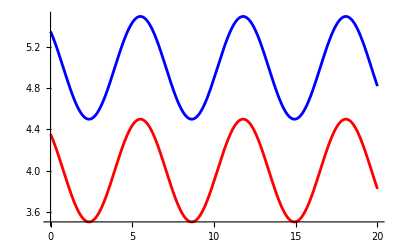

```mathematica
Plot[{Re[S1[0,t]/.values2] ,Im[S2[0,t]/.values2 ]},{t,0,20}, PlotStyle->{Blue,Red},PlotRange->All]
```

```mathematica
values1={hr-> 1,ω->1}
```

{hr→1,ω→1}

```mathematica
S1[0,0]
S2[0,0]
```

(a1 S10)/2+(b1 hr S10)/(2 √2)-ⅈ (-a2/2+b2) S20-(ⅈ b2 hr S20)/(2 √2)

ⅈ (a1/2-b1) S10+(ⅈ b1 hr S10)/(2 √2)+(a2 S20)/2+(b2 hr S20)/(2 √2)

```mathematica
solgen=  Extract[Solve[{(a1 S10)/2+(b1 hr S10)/(2 √2)==  Cos[θ],(a2 S20)/2+(b2 hr S20)/(2 √2)==2Sin[θ]},{S10,S20}, Assumptions->{a1∈ Reals,a2∈ Reals,b1∈ Reals,b2∈ Reals}],1]
```

{S10→(4 Cos[θ])/(2 a1+√2 b1 hr),S20→(8 Sin[θ])/(2 a2+√2 b2 hr)}

```mathematica
values3={hr-> 0.5,ω->1,a1-> -1, a2->1, b1-> 1,b2->1};
```

```mathematica
{Re[S1[0,tfin]/.solgen/. values3],Re[S2[0,tfin]/. solgen/.values3]}
```

{Re[(1.00872-0.0972773 ⅈ) Cos[θ]+(0.0929177-1.99167 ⅈ) Sin[θ]],Re[(0.0972773+4.10256 ⅈ) Cos[θ]+(1.99167+0.0929177 ⅈ) Sin[θ]]}

```mathematica
Do[points[θ][t_]= {-Re[S1[0,t]/. solgen /. values3],Re[S2[0,t]/.solgen/.values3]},{θ,0,2π,π/4}];
```

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding-> 1,PlotRange->{{-1.2,1.2},{-3,3}}(*,Axes -> True*)],Table[Graphics[{PointSize[Large],Blue,Point[points[θ][tfin]]}],{θ,0,2π,π/4}]] ]
```

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[ParametricPlot[{Re[-S1[0,tfin]/.solgen/. values3],Re[S2[0,tfin]/. solgen/.values3] },{θ,0,2π},PlotRangePadding-> 1,PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False]]
```

```mathematica
frames=Table[ParametricPlot[{Re[-S1[0,t]/. solgen/. values3],Re[S2[0,t]/. solgen/. values3]},{θ,0,2 π},PlotRangePadding->1,PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->True,AxesLabel->{Style["S1",White],Style["S2",White]},AxesStyle->White,TicksStyle->White,PlotStyle->{Purple,Thick},ImageSize->400, Background->Black,PlotLabel->Style["Circular Mode_Right = "<>ToString[NumberForm[t,{3,2}]],14,Bold,Black]],{t,0,10,0.1}   (*aquí defines el rango y paso del parámetro*)];

Export["\\Users\\cindy\\OneDrive/Desktop/circularder.gif",frames,"GIF"]
```

\Users\cindy\OneDrive/Desktop/circularder.gif